# Random matrix analysis of the v v^T linear setting

We illustrate here the random matrix analysis performed in the main material and the supplementary material. All notations are consistent with the ones presented in the text. Note that parts of the notebook are inter-dependent, so one should only run the notebook in the presented order.

In the whole notebook, one should take care to use preferably rational numbers rather than digits to keep a high working precision. For instance, write α = 1/10 instead of α=0.1.

All the quantities involved are defined in the supplementary material, in the random matrix analysis section, in the statement of the theorems or in the proofs.

```mathematica
ClearAll["Global`*"]
```

## Some auxiliary functions

We define some auxiliary functions that are going to be useful in the following.
We introduce the density ρ_Δ, with support [z_0, z_1]

```mathematica
ρ[Δ_,t_]:=(Sqrt[Δ]/(2*Pi))*Sqrt[4-Δ*(t+1/Δ)^2];
z0[Δ_]:=-1/Δ-2/Sqrt[Δ];
z1[Δ_]:=-1/Δ+2/Sqrt[Δ];
```

We introduce the integrals:
JnΔ[a,b] = Int[ρ_Δ(x) * x^n / (a+b*x)]
InΔ[a,b] = Int[ρ_Δ(x) * x^n / (a+b*x)^2]
They can be analytically computed:

```mathematica
J0Δ[Δ_,a_,b_]:=-(b-a Δ+√(-4 b^2 Δ+(b-a Δ)^2))/(2 b^2);
J1Δ[Δ_,a_,b_]:=(a b+2 b^2-a^2 Δ+a √(-4 b^2 Δ+(b-a Δ)^2))/(2 b^3);
I0Δ[Δ_,a_,b_]:=(Δ (-1+(-b+a Δ)/(√(-4 b^2 Δ+(b-a Δ)^2))))/(2 b^2);
I1Δ[Δ_,a_,b_]:=(3 a b Δ-2 a^2 Δ^2+b^2 (-1+4 Δ)-b √(-4 b^2 Δ+(b-a Δ)^2)+2 a Δ √(-4 b^2 Δ+(b-a Δ)^2))/(2 b^3 √(-4 b^2 Δ+(b-a Δ)^2));
I2Δ[Δ_,a_,b_]:=(2 a b+2 b^2-3 a^2 Δ+(2 a b^2 (1-4 Δ))/(√(-4 b^2 Δ+(b-a Δ)^2))-(5 a^2 b Δ)/(√(-4 b^2 Δ+(b-a Δ)^2))+(3 a^3 Δ^2)/(√(-4 b^2 Δ+(b-a Δ)^2)))/(2 b^4);
```

```mathematica
(*A test of the previous expressions taking random Δ, a and b, checking that a+z0[Δ]*b > 0*)
Δ=RandomReal[10];
a=RandomReal[];
b=RandomReal[-a/z0[Δ]];
NIntegrate[ρ[Δ,t],{t,z0[Δ],z1[Δ]}];
J0N=Abs[NIntegrate[ρ[Δ,t]/(a+b*t),{t,z0[Δ],z1[Δ]}]-J0Δ[Δ,a,b]];
J1N=Abs[NIntegrate[ρ[Δ,t]*t/(a+b*t),{t,z0[Δ],z1[Δ]}]-J1Δ[Δ,a,b]];
I0N=Abs[NIntegrate[ρ[Δ,t]/(a+b*t)^2,{t,z0[Δ],z1[Δ]}]-I0Δ[Δ,a,b]];
I1N=Abs[NIntegrate[ρ[Δ,t]*t/(a+b*t)^2,{t,z0[Δ],z1[Δ]}]-I1Δ[Δ,a,b]];
I2N=Abs[NIntegrate[ρ[Δ,t]*t^2/(a+b*t)^2,{t,z0[Δ],z1[Δ]}]-I2Δ[Δ,a,b]];
satisfied=Max[J0N,J1N,I0N,I1N, I2N];
If[satisfied≤10^(-8),Print["All auxiliary functions are correct !"];, Print["ERROR"];];
ClearAll[a,b,Δ,J0N,J1N,I0N,I1N, I2N,satisfied];
```

All auxiliary functions are correct !

## Computing the eigenvalue density

We show here how to compute the asymptotic spectral density ν(α,Δ).
We first introduce its inverse Stieltjes transform:

```mathematica
InverseStieltjes[α_,Δ_,s_]:=-1/s+α*J1Δ[Δ,1,s];
```

We can also numerically compute the Stieltjes transform of ν. To do this, we numerically solve the implicit equation InverseStieltjes[α,Δ,s] = z. It can be rewritten as g[z] + (z - α*J1Δ[Δ,1,s])^{-1} = 0, and this last form turns out to be numerically more stable than InverseStieltjes[α,Δ,s] = z for numerical root finding.
Using the Stieltjes-Perron inversion theorem, we add a small imaginary part ϵ to z and actually compute g(z+ⅈ*ϵ). For z inside the support of ν, we will then access the density of ν, while for z outside of the support, this will give us g(z).

```mathematica
(*An auxiliary function, that we have to zero to get the Stieltjes transform*)
H[α_,Δ_,z_,s_]:=s+ (z-α*J1Δ[Δ,1,s])^(-1);
```

```mathematica
(*Note that z = 0 can cause problems in the computation of the density, so one should avoid it*)
Stieltjes[α_,Δ_,z_]:=Module[{Sol,gr,gi,ϵ,satisfied,start},
ϵ=10^(-10); (*The small imaginary part*)
start = -100; (*A starting point for the root searching*)
If[z≠0, start=-1/z];
(*We use a great working precision to prevent numerical problems*)
Sol = FindRoot[{Re[H[α,Δ,z+ⅈ*ϵ,sr+ⅈ*si]],Im[H[α,Δ,z+ⅈ*ϵ,sr+ⅈ*si]]},{sr,start},{si,1},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20];
gr=sr/.Sol;
gi=si/.Sol;
satisfied=Abs[H[α,Δ,z+ⅈ*ϵ,gr+ⅈ*gi]];
{gr+ⅈ*gi,satisfied}
];
(*It returns g[z+ⅈ*ϵ] as well as a value that allows us to check if the root finding worked*)
```

From the Stieltjes transform we can directly compute the density of ν :

```mathematica
ν[α_,Δ_,z_]:=Module[{stieltjes,g,satisfied},
stieltjes=Stieltjes[α,Δ,z];
g=stieltjes[[1]];
satisfied=stieltjes[[2]];
If[Abs[satisfied]>10^(-5),Print["ERROR IN THE COMPUTATION OF THE STIELTJES TRANSFORM AT z = ", z]];
Im[g]/Pi
];
```

```mathematica
PlotBulk[α_,Δ_,zinf_,zmax_,step_]:=Module[{zvalues,bulkvalues,pos0},
zvalues=Range[zinf,zmax,step];
(*We remove z = 0 for numerical issues*) 
pos0=Position[zvalues,0];
If[pos0≠{},zvalues=Delete[zvalues, pos0[[1,1]]]];
bulkvalues=Table[ν[α,Δ,z],{z,zvalues}];
ListLinePlot[Transpose[{zvalues,bulkvalues}],PlotStyle->{Red,Thick}]
];
```

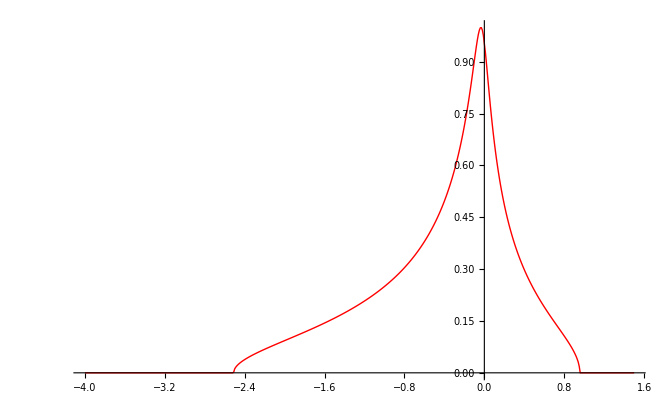

```mathematica
(*One should avoid using digits with small working precision and use rational numbers instead*)
α=2;
Δ=5;
zinf=-4;
zmax=15/10;
step=1/100;
PlotBulk[α,Δ,zinf,zmax,step]
ClearAll[α,Δ,zinf,zmax,step]
```

We can benchmark the bulk computation by doing an histogram of the eigenvalue density by generating a large random matrix and comparing its eigenvalue histogram with the density.

```mathematica
BenchmarkBulk[α_,Δ_,zinf_,zmax_,step_]:=Module[{zvalues,bulkvalues,pos0,k,p,W,ξ,Γk,eigenvalues},
(*First we compute again the bulk analytically*)
zvalues=Range[zinf,zmax,step];
(*We remove z = 0 for numerical issues*) 
pos0=Position[zvalues,0];
If[pos0≠{},zvalues=Delete[zvalues, pos0[[1,1]]]];
bulkvalues=Table[ν[α,Δ,z],{z,zvalues}];
(*Now we numerically generate a large random matrix*)
k=1000;
p=IntegerPart[k*α];
(*The W matrix*)
W=Table[RandomVariate[NormalDistribution[]],{i,1,p},{l,1,k}];
(*The ξ matrix*)
ξ=Table[RandomVariate[NormalDistribution[]]/Sqrt[p],{i,1,p},{j,1,p}];
Do[ξ[[i,i]]*=Sqrt[2],{i,1,p}];  (*The variance of diagonal elements is twice as big*)
Do[ξ[[i,j]]=ξ[[j,i]],{i,1,p},{j,1,i-1}];  (*Symmetry*)
(*Constructing the Γk matrix *)
Γk=(1/k)*Transpose[W].(ξ/Sqrt[Δ]-(1/Δ)*IdentityMatrix[p]).W;
eigenvalues=Eigenvalues[Γk];
(*Plotting a comparison of the two*)
Show[{Histogram[eigenvalues,50,"PDF"],ListLinePlot[Transpose[{zvalues,bulkvalues}],PlotStyle->{Red,Thick},PlotRange->All]}]
];
```

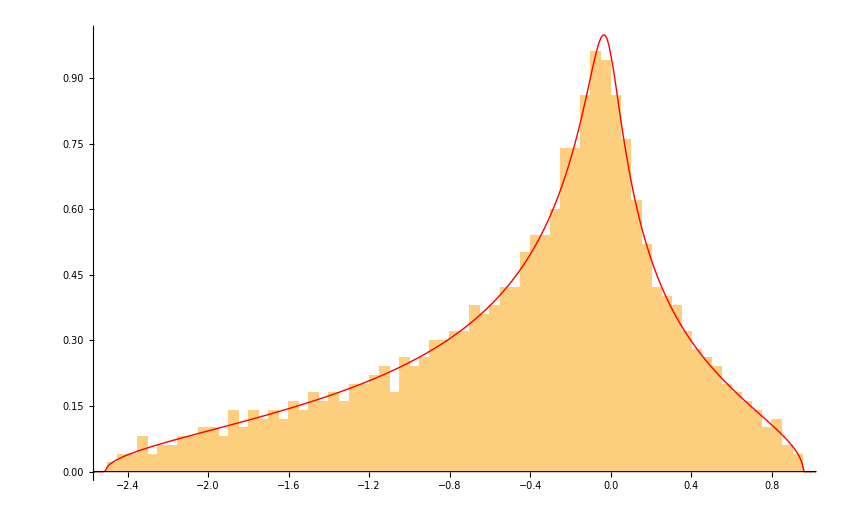

```mathematica
(*The generation of large matrices can take a few seconds/minutes*)
α=2;
Δ=5;
zinf=-4;
zmax=15/10;
step=1/100;
BenchmarkBulk[α,Δ,zinf,zmax,step]
ClearAll[α,Δ,zinf,zmax,step]
```

## Computing λmax

Computing λmax requires computing s_edge. 
We first introduce the function F[α,Δ,s] = α*Int[ρ_Δ(t) * (st/(1+st))^2]. We must solve for F[α,Δ,s] = 1 to find s_edge as seen in the supplementary material.

```mathematica
F[α_,Δ_,s_]:=α*s^2*I2Δ[Δ,1,s];
MinusOneOver[x_]:=-1/x;
```

Now we can introduce a function s_edge and a function λmax

```mathematica
sedge[α_,Δ_]:=Module[{SimplifiedEq,Solution,edge,satisfied,svalues,svalue},
SimplifiedEq[s_]:=Simplify[F[α,Δ,s]]; (*We simplify the equation using the values of α,Δ*)
Solution=NSolve[SimplifiedEq[s]==1,{s}];
svalues={};
Do[
svalue=s/.sol;
(*We discard the possible s=0 solution*)
If[Abs[svalue]≥10^(-5),
satisfied=Abs[SimplifiedEq[svalue]-1];
If[Abs[Im[svalue]]≤10^(-5)&&satisfied≤10^(-3), 
(*We discard solutions that are not real*)
svalue=Re[svalue];
AppendTo[svalues,svalue];
];
];
,{sol,Solution}];
(*Now we take the negative s closest to 0, so the one for which -1/s is the biggest*)
svalue=MaximalBy[svalues,MinusOneOver][[1]];
svalue
];
```

```mathematica
λmax[α_,Δ_]:=InverseStieltjes[α,Δ,sedge[α,Δ]];
```

We can plot the first and second eigenvalues of Γk. Thanks to our theorem, we know that an eigenvalue equals to 1 detaches at Δ = Δc(α) = 1+α.

```mathematica
Δc[α_]:=1+α;
```

```mathematica
Plotλ1λ2[α_]:=Module[{ΔList,λ1,λ2,λmaxvalue},
ΔList=Range[5/10,5,5/100];
λ1={};
λ2={};
Do[
λmaxvalue=λmax[α,Δ];
AppendTo[λ2,λmaxvalue];
If[Δ≥Δc[α],
AppendTo[λ1,λmaxvalue];
,
AppendTo[λ1,1];
];
,{Δ,ΔList}];
ListLinePlot[{Transpose[{ΔList,λ1}],Transpose[{ΔList,λ2}]},PlotStyle->{Red,Blue},PlotLegends->{"λ1", "λ2"},PlotRange->{{5/10,5},{0.5,1.1}},AxesLabel->{"Δ","λ"}]
];
```

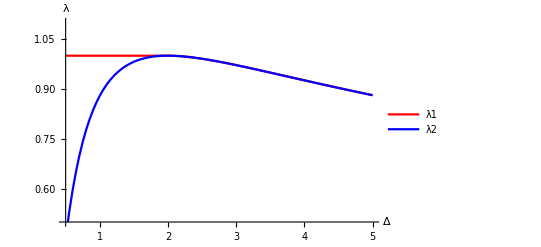

```mathematica
(*Use rational numbers*)
α=1;
Plotλ1λ2[α]
ClearAll[α];
```

## Computing ϵ(Δ)

We compute here the squared correlation ϵ(Δ). We first define the auxiliary functions T^(r)[s] and T^(r,q)[s] (counterparts of the functions S^(r)[λ] and S^(r,q)[λ]) introduced in the supplementary material, in the proof of the transition.

```mathematica
(*The derivative of the inverse Stieltjes transform*)
DInverseStieltjesexpr=FullSimplify[D[InverseStieltjes[α,Δ,s],s],α>0&&Δ>0&&s<0];
DInverseStieltjes[α_,Δ_,s_]:=Evaluate[DInverseStieltjesexpr];
```

```mathematica
(*The auxiliary functions*)
(*This can take some time as we simplify some expressions*)
T1[α_,Δ_,s_]:=s*(α-(1+s*InverseStieltjes[α,Δ,s]) );
DT1expr=FullSimplify[D[T1[α,Δ,s],s],α>0&&Δ>0&&s<0];
DT1[α_,Δ_,s_]:=Evaluate[DT1expr];
T2[α_,Δ_,s_]:=s*(α*(1+α)-(1+2*α)*(1+s*InverseStieltjes[α,Δ,s]) +(1+s*InverseStieltjes[α,Δ,s])^2 );
DT2expr=FullSimplify[D[T2[α,Δ,s],s],α>0&&Δ>0&&s<0];
DT2[α_,Δ_,s_]:=Evaluate[DT2expr];
(*Introducing the T3 function*)
T3[α_,Δ_,s_]:=s*(α+3*α^2+α^3-(1+5*α+3*α^2)*(1+s*InverseStieltjes[α,Δ,s]) +(2+3*α)*(1+s*InverseStieltjes[α,Δ,s])^2 - (1+s*InverseStieltjes[α,Δ,s])^3 );
DT3expr=FullSimplify[D[T3[α,Δ,s],s],α>0&&Δ>0&&s<0];
DT3[α_,Δ_,s_]:=Evaluate[DT3expr];
(*T11*)
T11[α_,Δ_,s_]:=s*T2[α,Δ,s]-(1+s*InverseStieltjes[α,Δ,s])*DT1[α,Δ,s]/DInverseStieltjes[α,Δ,s]+α*s*(s+T1[α,Δ,s])*(I2Δ[Δ,1,s]*DT1[α,Δ,s]/DInverseStieltjes[α,Δ,s]-I1Δ[Δ,1,s]*s);
(*T12*)
T12[α_,Δ_,s_]:=s*T3[α,Δ,s]-(1+s*InverseStieltjes[α,Δ,s])*(T11[α,Δ,s]+(1+α)*DT1[α,Δ,s]/DInverseStieltjes[α,Δ,s])+α*s*((1+α)*s+T1[α,Δ,s]+T2[α,Δ,s])*(I2Δ[Δ,1,s]*DT1[α,Δ,s]/DInverseStieltjes[α,Δ,s]-I1Δ[Δ,1,s]*s);
```

```mathematica
Plotϵ[α_]:=Module[{ΔList,ϵList,Δ,g1},
ΔList=Range[1/1000,Δc[α],1/100];
ϵList=Table[0,{Δ,ΔList}];
Do[
Δ=ΔList[[i]];
(*The stieltjes transform at z=1*)
g1=Re[Stieltjes[α,Δ,1][[1]]];
ϵList[[i]]=α*Δ^2/T12[α,Δ,g1];
,{i,1,Length[ΔList]}];
ListLinePlot[Transpose[{ΔList,ϵList}],PlotLegends->{"ϵ(Δ)"},AxesLabel->{"Δ",""},PlotStyle->Thick]
];
```

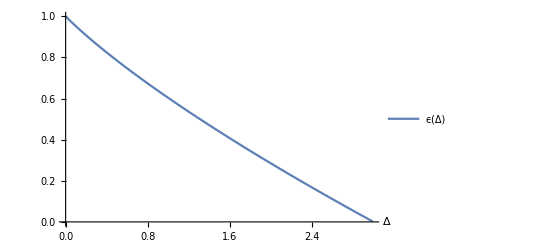

```mathematica
(*Use rational numbers to keep a high working precision*)
α=20/10;
Plotϵ[α]
ClearAll[α];
```

## Some analytical computations used in the proof

We enumerate here some relations used in the proof. They must obviously be checked without the use of an engine, but Mathematica’s formal calculation power gives a nice consistency check.

We use in the proof the value of α * Int[ρ_Δ(t) * (ts/(1+ts))^2] taken at s = -1, for Δ>1 . One can check it here.

```mathematica
FullSimplify[F[α,Δ,-1],α>0&&Δ>1]
```

α/(-1+Δ)

We use the partial derivative dz/dΔ in the proof. Recall that z = InverseStieltjes[α,Δ,s]

```mathematica
Together[FullSimplify[D[InverseStieltjes[α,Δ,s],Δ],α>0&&Δ>0&&s<0]]
```

-(α (s+2 s^2-Δ+√(s^2-2 s Δ-4 s^2 Δ+Δ^2)))/(2 s^3 √(s^2-2 s Δ-4 s^2 Δ+Δ^2))

Check that the largest eigenvalue at Δ = Δc[α] is z_edge=1, or equivalently InverseStieltjes[α, Δc[α], -1] = 1

```mathematica
FullSimplify[InverseStieltjes[α,Δc[α],-1],α>0]
```

1

An identity on the function T2 that we use in the proof of the eigenvalue transition can be checked explicitly

```mathematica
FullSimplify[(T2[α,Δ,s]+α*Δ)/(InverseStieltjes[α,Δ,s]-1),α>0&&Δ>0&&s<0]
```

(α (s-Δ-2 s Δ+√(s^2-2 s (1+2 s) Δ+Δ^2)))/(2 (1+s))

```mathematica
FullSimplify[T2[α,Δ,-1],α>0&&Δ>0]
```

Piecewise[{{-α (1+α), Δ≥1}, {-α Δ (1+α Δ), True}}]

Another consistency check : T12[α, Δc[α], -1] = + Infinity

```mathematica
FullSimplify[1/T12[α,Δc[α],-1],α>0]
```

0

The limit Δ->0 of T12[s]

```mathematica
FullSimplify[Series[T12[α,Δ,s],{Δ,0,2}],α>0&&Δ>0&&s<0]
```

α Δ^2+O[Δ]^3

In the case α = 1 (at the end of the eigenvector correlation proof), we must compute the limit of T12[s] * DInverseStieltjes[s] when s -> s_edge and show that this limit is strictly positive. 
We can use many simplifications coming from the definitions of s_edge.
 For instance, I2Δ[Δ,1,s_edge] = 1/(α*s_edge^2) = 1/(s_edge^2) by definition of s_edge and since α = 1.
The only terms that remain in the limit s -> s_edge are the following:

```mathematica
coefDT1=1-(1+s*InverseStieltjes[1,Δ,s])-s*InverseStieltjes[1,Δ,s];
coeffT11=-(1+s*InverseStieltjes[1,Δ,s])*coefDT1+s*(s+T1[1,Δ,s])*(coefDT1/(1*s^2));
(*coeffT12 is the limit of T12[s]*DInverseStieltjes[s] when s->sedge, replacing s by sedge*)
coeffT12=-(1+s*InverseStieltjes[1,Δ,s])*(coeffT11+(1+1)*coefDT1)+s*((1+1)*s+T1[1,Δ,s]+T2[1,Δ,s])*(coefDT1/(s^2));
```

```mathematica
FullSimplify[coeffT12,s<0&&Δ>0]
```

((s (-3+4 s)+3 Δ-3 √(s^2-2 s (1+2 s) Δ+Δ^2)) (s-Δ+√(s^2-2 s (1+2 s) Δ+Δ^2))^2)/(4 s^6)

We can check that there is no real negative solutions to coeffT12 = 0 for Δ > 1

```mathematica
Reduce[coeffT12==0&&s<0&&Δ>1,s]
```

False